5

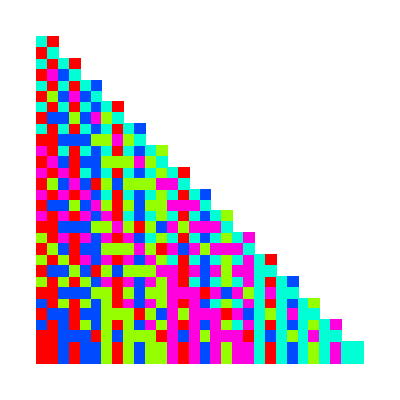

```mathematica
A000217[n_]:=Binomial[n+1,2];
A003056[n_]:=Floor[(Sqrt[1+8n]-1)/2]
A002262[n_]:=n-A000217[A003056[n]]
Design[x_,y_]:=Module[{a,b,r,colors},
a=x; b=x+y;r=0.5;
colors=Hue[N[(1+√5)/2]*#]&/@{
A003056[b],A002262[a],
A003056[a],A002262[b]
};
Riffle[colors,{
Rectangle[{x-r,y},{x,y+r}],Rectangle[{x,y},{x+r,y+r}],
Rectangle[{x-r,y-r},{x,y}],Rectangle[{x,y-r},{x+r,y}]
}]
]
k=5 (* Number of colors *)
Graphics[Table[Design[x,y],{x,0,Binomial[k+1,2]-1},{y,0,Binomial[k+1,2]-1-x}]]
```

```mathematica
(*SeedRandom[0];*)
Design2[α_,β_,θ_]:=Module[{x,y,a,b,r,colors},
x=α+β/2;y=(√3)/2 β;
a=α; b=α+β;r=0.5;

colors=Hue[N[(1+√5)/2]*#]&/@{
A003056[b],A002262[a],
A003056[a],A002262[b]
};
(*θ=RandomReal[]*2π;*)
Riffle[colors,{
Disk[{x,y},r,{π/2+θ,π+θ}],Disk[{x,y},r,{0+θ,π/2+θ}],
Disk[{x,y},r,{π+θ,3π/2+θ}],Disk[{x,y},r,{3π/2+θ,2π+θ}]
}]
]
k=7(* Number of colors *)
Manipulate[
Graphics[Table[Design2[x,y,θ],{x,0,Binomial[k+1,2]-1},{y,0,Binomial[k+1,2]-1-x}],Background->Black,ImageSize->Large],
{θ,0,2π}
]
```

7

```mathematica
Table[
Binomial[Binomial[n+1,2]+1,3],{n,0,10}
]
```

{0,0,4,35,165,560,1540,3654,7770,15180,27720}

```mathematica
Binomial[Binomial[n+1,2]+2,3]//Expand
(n*(n+1)*(n^2+n+2)*(n^2+n+4))/48//Expand
```

n/6+(7 n^2)/24+(13 n^3)/48+(3 n^4)/16+n^5/16+n^6/48

n/6+(7 n^2)/24+(13 n^3)/48+(3 n^4)/16+n^5/16+n^6/48

```mathematica
Table[
Binomial[Binomial[n+1,2]+3,4],
{n,0,10}
]
```

{0,1,15,126,715,3060,10626,31465,82251,194580,424270}